```mathematica
r1=1;r2=1/0.162;r2=1/0.163;
σ=0.0036;
γ=0.02; a=0.2;
```

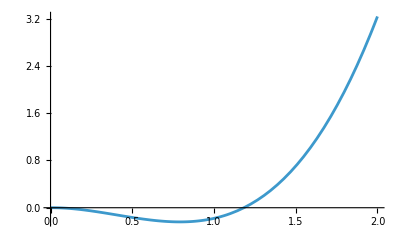

```mathematica
f[v_]=v(1-v)(v-a);
Plot[-f[v]-σ v/γ,{v,0,2}]
eqn=FindRoot[-f[v]-σ v/γ==0,{v,0.1}];
smallroot=v/.eqn;
vinf=smallroot/2;
```

NDSolveValue::ndsz: At x == -0.0697196, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

Best β: 1.04529

Best xstar: 560029/2097152

-0.0316504

Best β: 1.67946

Best xstar: 829215/2097152

-0.0213746

Best β: 2.32191

Best xstar: 1016681/2097152

-0.0174324

Best β: 2.84

Best xstar: 1104953/2097152

-0.0160393

Best β: 3.2075

Best xstar: 1140631/2097152

-0.0155374

Best β: 3.44451

Best xstar: 1155211/2097152

-0.0153412

Best β: 3.58478

Best xstar: 1161549/2097152

-0.0152575

Best β: 3.66235

Best xstar: 1164465/2097152

-0.0152193

Best β: 3.70336

Best xstar: 1165857/2097152

-0.0152011

Best β: 3.72448

Best xstar: 1166537/2097152

-0.0151922

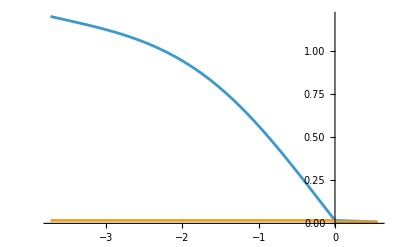

```mathematica
K=1.2;
mmin=-2;
mmax=-0.1;
For[j=0,j<10,j=j+1,
m=(mmax+mmin)/2;
bmax=5;bmin=0.8;
For[k=0,k<20,k=k+1,
β=(bmax+bmin)/2;
{V1,U1}=NDSolveValue[{v'[x]==u[x],r1 u'[x]==-f[v[x]]-σ v[x]/γ,v[-β]==K,u[-β]==m},{v,w},{x,-β,0}];
If[V1[0]>smallroot,bmin=β,bmax=β];
];
β=(bmax+bmin)/2;
Print["Best β: ",β];
{V1,U1}=NDSolveValue[{v'[x]==u[x],r1 u'[x]==-f[v[x]]-σ v[x]/γ,v[-β]==K,u[-β]==m},{v,w},{x,-β,0}];

xstarmax=1;
xstarmin=0;
For[k=0,k<20,k=k+1,
xstar=(xstarmax+xstarmin)/2;
{V2,U2}=NDSolveValue[{v'[x]==u[x],r2 u'[x]==-f[v[x]]-σ v[x]/γ,v[0]==smallroot,u[0]==(r1^2/r2^2) V1'[0]},{v,w},{x,0,xstar}];
If[V2[xstar]>vinf,xstarmin=xstar,xstarmax=xstar];
];
xstar=(xstarmax+xstarmin)/2;
Print["Best xstar: ",xstar];
{V2,U2}=NDSolveValue[{v'[x]==u[x],r2 u'[x]==-f[v[x]]-σ v[x]/γ,v[0]==smallroot,u[0]==(r1^2/r2^2) V1'[0]},{v,w},{x,0,xstar}];
If[V2'[xstar]>0,mmax=m,mmin=m];
Print[V2'[xstar]]
]
Show[Plot[{V1[x],smallroot},{x,-β,0}],Plot[{V2[x],vinf},{x,0,xstar}],PlotRange->All]
```

```mathematica
v
```